```mathematica
m=16;
n=10000;
error[k_]:=((Binomial[m+k,k]+1)/n)^((k+1)/m);
Array[error,5]//N
```

{0.453847,0.457257,0.558075,0.797411,1.3053}

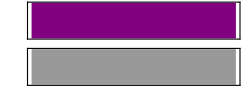

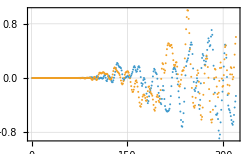

```mathematica
sound=Sound[SoundNote["G",0.002,"Piano"]]
list=AudioData@sound;
ListPlot[list, PlotTheme->"Detailed"]
```

```mathematica
list//Dimensions
```

{2,640}

```mathematica
f=2π*440.;
α=2.^(1/12);
play=Play[Sin[f t]+Sin[f α^3 t]+Sin[f α^7 t],{t,0,4}]
```

-Graphics-

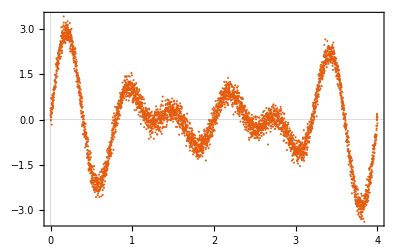

```mathematica
signal=Table[Sin[2π t]+Sin[2π t*1.25]+Sin[2π t*1.5],{t,0,4,0.001}];
𝒫=WhiteNoiseProcess[0.2];
noise=RandomFunction[𝒫,{1,Length@signal}];
noise=Normal[noise][[1,;;,2]];
ListPlot[signal+noise,DataRange->{0,4},PlotTheme->"Scientific"]
```

```mathematica
noise=RandomFunction[𝒫,{0,Length@signal}];
noise=Normal[noise][[1,;;,2]];
noise//Dimensions
```

{402}

```mathematica
Play[Sin[f t]+Sin[f *1.2 t]+Sin[f *1.5 t],{t,0,4}]
```

-Graphics-

```mathematica
data=Table[{x,y,Exp[Sin[π x]+y^2]+0.*RandomVariate[NormalDistribution[]]},{x,-1,1,0.02},{y,-1,1,0.02}];
data=Flatten[data,1];
Echo@Dimensions@data;
ListPointPlot3D[data,PlotTheme->"Detailed"]
```

{10201,3}

-Graphics3D-

```mathematica
Binomial[8,3]
```

56

```mathematica
P=97;
Plot3D[Mod[x-y,P],{x,0,97},{y,0,97},PlotTheme->"Scientific",PlotRange->Full(*,PlotPoints->300*)]
```

-Graphics3D-

```mathematica
Plot3D[Mod[x-y,1],{x,0,1},{y,0,1},PlotTheme->"Scientific",PlotRange->Full]
```

-Graphics3D-

```mathematica
Binomial[10,4]
```

210

```mathematica
f[x_,y_]:=With[{r=Sqrt[x^2+y^2],θ=ArcTan[x,y]},BesselJ[6,20 r] Cos[6 θ]];

(*Plot with publication settings*)
plt=Plot3D[f[x,y],{x,-1,1},{y,-1,1},PlotTheme->"Business",PlotPoints->200,ImageSize->90,AxesLabel->{"", "", ""},
Ticks->{{-1,0,1}, {-1,0,1}, {-0.3, 0, 0.3}}, TicksStyle->Directive[FontFamily->"Helvetica",8],LabelStyle->Directive[FontFamily->"Helvetica",8],Boxed->True,BoxStyle->AbsoluteThickness[0.75],Mesh->None]
```

-Graphics3D-

```mathematica
Export["/Users/hongyi/Desktop/cyl_harmonic.png",plt,"png",(*ImageSize->120,*) ImageResolution->1000]
```

/Users/hongyi/Desktop/cyl_harmonic.png

```mathematica
Plot3D[(x y)/(x^2+y^2),{x,-1,1},{y,-1,1},PlotTheme->"Business",PlotPoints->200]
```

-Graphics3D-

```mathematica
Integrate[(a x+b y+c)^2,{x,-1,1},{y,-1,1}]
```

4/3 (a^2+b^2+3 c^2)

```mathematica
2^16
```

65536

```mathematica
131072*16/512
```

4096

## Scaling law wrt width

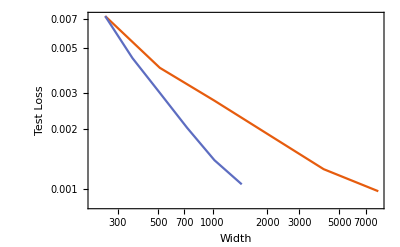

```mathematica
dlist={256, 512, 1024,2048, 4096, 8192};
dstoplist=Round[16 √#]&/@dlist;
loss={7.225*^-3, 4.006*^-3, 2.753*^-3, 1.862*^-3, 1.260*^-3, 9.796*^-4};
losscp={7.225*^-3, 4.473*^-3, 3.010*^-3, 2.020*^-3, 1.396*^-3, 1.060*^-3};
ListLogLogPlot[{Transpose@{dlist, loss}, Transpose@{dstoplist, losscp}}, Joined->True,PlotTheme->"Scientific", FrameLabel->{"Width", "Test Loss"}]
```

```mathematica
FindFit[Transpose@{dlist, loss}, L0+(x0/x)^α,{L0,x0,α},x]
```

{L0→0.00076914,x0→0.934818,α→0.899932}

```mathematica
FindFit[Transpose@{dstoplist, losscp}, (x0/x)^α,{L0,x0,α},x]
```

{L0→1.,x0→4.34725,α→1.2136}

```mathematica
2^17
```

131072